```mathematica
f[x_]:=PDF[1/10,x]
```

```mathematica
f[1]
```

PDF[1/10,1]

```mathematica
6!/(4!*2!)
```

15

```mathematica
h1[P_]:=(-941.254840173)+(0.014460465765)*P+(-9.415297264511*10^-05)*P^2+(1.23485231253*10^-06)*P^3
h2[P_]:=(-941.254313412)+(0.014234188877)*P+(-0.00013455013645)*P^2+(2.58697027372*10^-06)*P^3
```

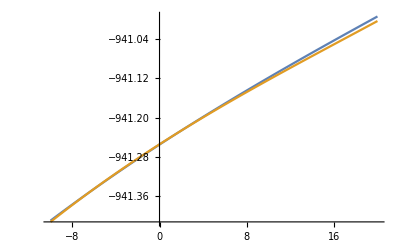

```mathematica
Plot[{h1[x],h2[x]},{x,-10,20}]
```

```mathematica
Solve[h1[x]-h2[x]==0,{x}]
```

{{x→-6.32436},{x→1.79012},{x→34.4112}}

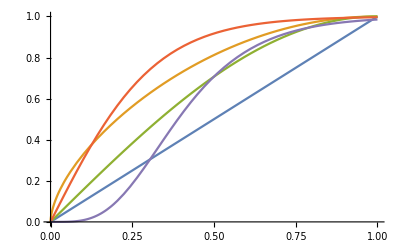

```mathematica
Plot[{x,Sin[x*Pi*0.5]^0.6,Sin[x*Pi*0.5],Tanh[x*Pi],Tanh[x*Pi]^4},{x,0,1}]
```

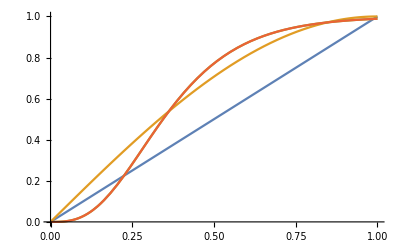

```mathematica
Plot[{x,Sin[x*Pi*0.5],Tanh[x*Pi]^3,(Exp[x*Pi]-Exp[-x*Pi])^3/(Exp[x*Pi]+Exp[-x*Pi])^3},{x,0,1}]
```

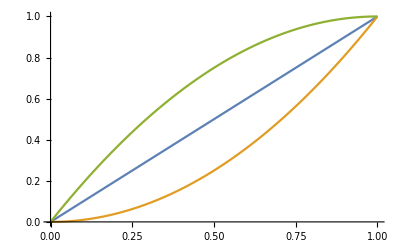

```mathematica
Plot[{x,x^2,x+(x-x^2)},{x,0,1}]
```

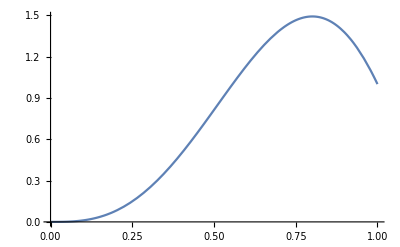

```mathematica
Plot[x^3*(4-3x^2)*(3-2x),{x,0,1}]
```

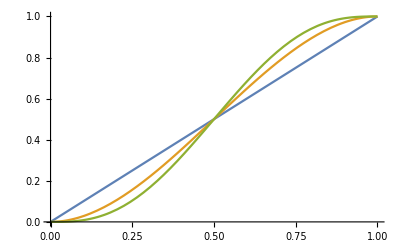

```mathematica
Plot[{x,x^2*(3-2x),6x^5+-15*x^4+10x^3},{x,0,1}]
```

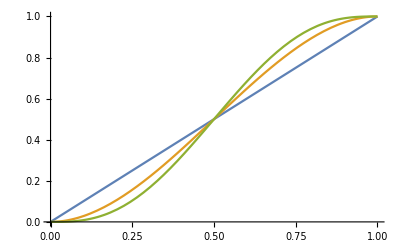

```mathematica
Plot[{x,x^2*(3-2x),x^3*(x*(6x-15)+10)},{x,0,1}]
```

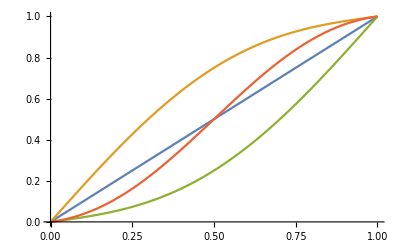

```mathematica
Plot[{x,0.25Sin[1*Pi*x]+x,-0.25Sin[1*Pi*x]+x,(0.25Sin[1*Pi*x]+x)*x+(1-x)*(-0.25Sin[1*Pi*x]+x)},{x,0,1}]
```

```mathematica
Plot[{x,0.25Sin[1*Pi*x]+x,-0.25Sin[1*Pi*x]+x,(0.25Sin[1*Pi*x]+x)*x+(1-x)*(-0.25Sin[1*Pi*x]+x)},{x,0,1}]
```

-Graphics-

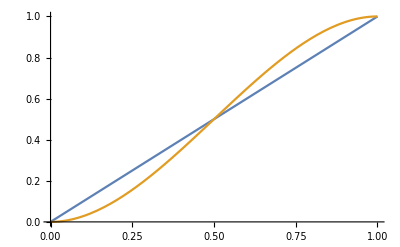

```mathematica
Plot[{x,x^2*(1-x)+x*(x+(x-x^2))},{x,0,1}]
```

```mathematica
Plot[{x,x^2*(1-x)+x*(x+(x-x^2))},{x,0,1}]
```

-Graphics-

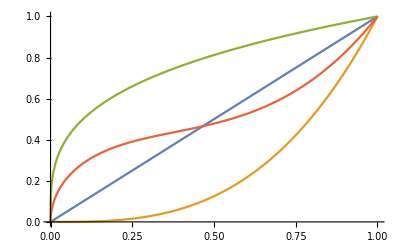

```mathematica
Plot[{x,x^3,1/x^-0.3,x^2*x+(1-x)*x^(1/2)},{x,0,1}]
```

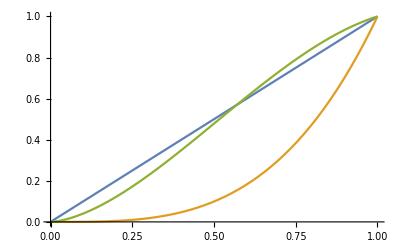

```mathematica
Plot[{x,x^3/x^-(1/3),x^2*(1-x)+x*x^(1/2)},{x,0,1}]
```

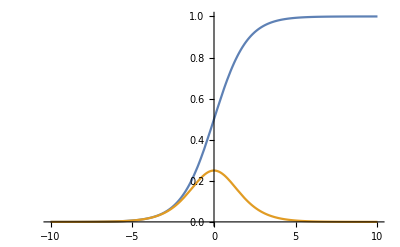

```mathematica
Plot[{1/(1+Exp[-x]),Evaluate@D[1/(1+Exp[-x]),x]},{x,-10,10}]
```

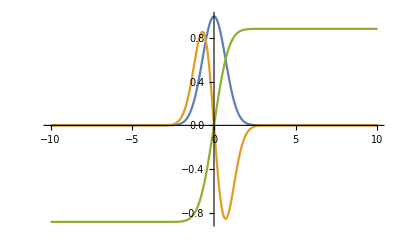

```mathematica
Plot[{Exp[-x^2],Evaluate@D[Exp[-x^2],x],Evaluate@Integrate[Exp[-x^2],x]},{x,-10,10},PlotRange->All]
```

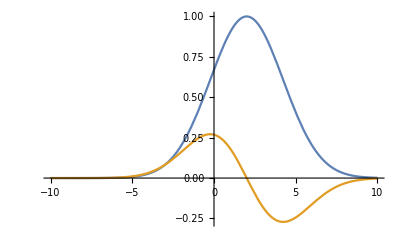

```mathematica
Plot[{Exp[-(x-2)^2/10],Evaluate@D[Exp[-(x-2)^2/10],x]},{x,-10,10}]
```

```mathematica
Integrate[Exp[-(x-2)^2/10]*DiracDelta[x-y],{x,-∞,∞}]
```

ConditionalExpression[ⅇ^(-1/10 (-2+y)^2),y∈Reals]

```mathematica
Integrate[Exp[-(x-2)^2/10]*(x-y)^2,{x,-∞,∞}]
```

√(10 π) (9+(-4+y) y)

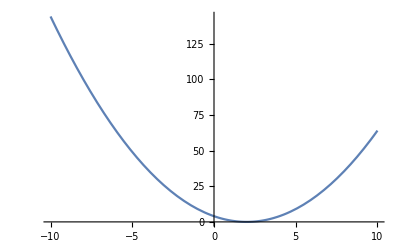

```mathematica
Plot[(2-y)^2,{y,-10,10}]
```

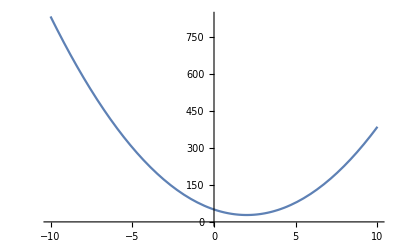

```mathematica
Plot[%,{y,-10,10}]
```

```mathematica
g[y_]:=y*(1-y)
```

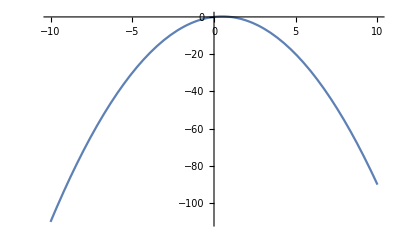

```mathematica
Plot[g[a],{a,-10,10}]
```

```mathematica
Evaluate@Integrate[(1/(1+Exp[-a])),a]
```

Log[1+ⅇ^a]

```mathematica
Evaluate@D[(1/(1+Exp[-a])),a]
```

ⅇ^-a/((1+ⅇ^-a)^2)

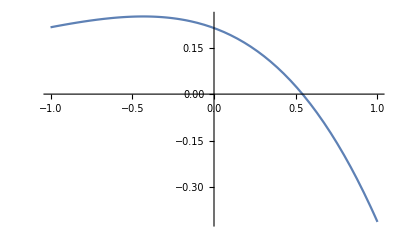

```mathematica
Plot[g[Log[1+ⅇ^a]],{a,-1,1}]
```

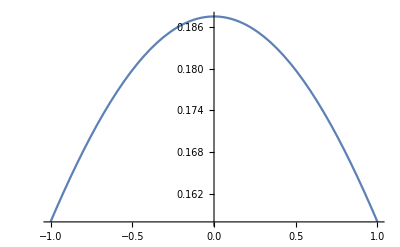

```mathematica
Plot[g[ⅇ^-a/((1+ⅇ^-a)^2)],{a,-1,1}]
```

```mathematica
listmeamzr=ReadList["/Volumes/MicroSD/2_PostDoc_SD/tmp/meam_zr_4850_fc.txt",Number];
listdftzr=ReadList["/Volumes/MicroSD/2_PostDoc_SD/tmp/dft_zr_4850_fc.txt",Number];
listmeamc=ReadList["/Volumes/MicroSD/2_PostDoc_SD/tmp/meam_c_4850_fc.txt",Number];
listdftc=ReadList["/Volumes/MicroSD/2_PostDoc_SD/tmp/dft_c_4850_fc.txt",Number];
```

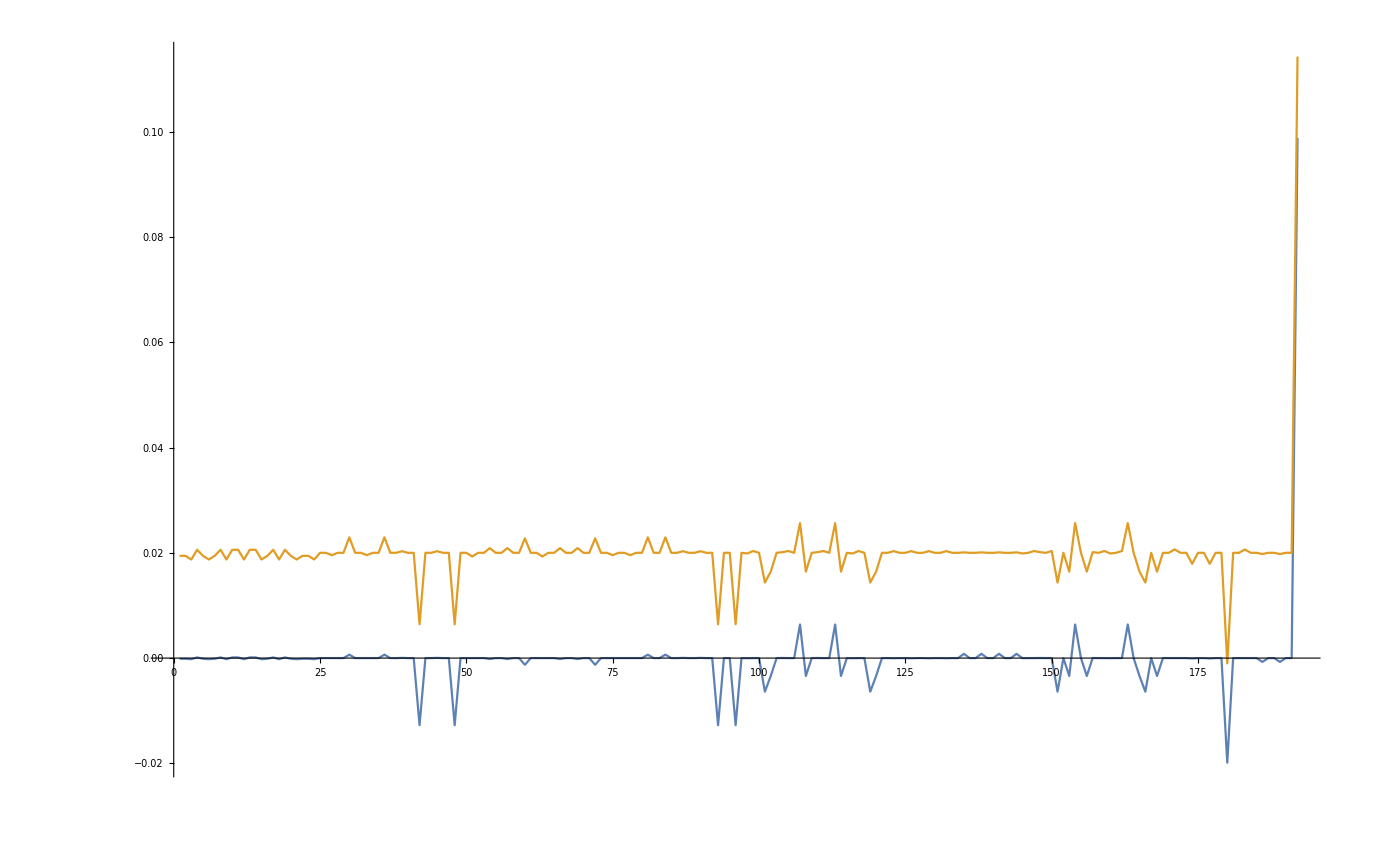

```mathematica
ListLinePlot[{listmeamzr,listdftzr+0.02},PlotRange->All]
```

```mathematica
Norm[1*listmeamc-listdftc]
```

0.013359

```mathematica
Minimize[Norm[a*listmeamc-listdftc],a]
```

{0.0133386,{a→1.00547}}

```mathematica
Norm[1*listmeamzr-listdftzr]
```

0.0107054

```mathematica
Minimize[Norm[a*listmeamzr-listdftzr],a]
```

{0.00994078,{a→0.962519}}

```mathematica
Norm[1.0054656340714538*listmeamc-listdftc]
```

0.0133386

```mathematica
Norm[listmeamzr-listdftzr]
```

0.0107054

```mathematica
list[[1]]
Total@list[[2;;-1]]
```

0.12347792426027122

-0.123478

```mathematica
Total@listdft
```

1.54363×10^-8

```mathematica
{list-listdft}[[1]][[1]]
```

0.00217303261190162

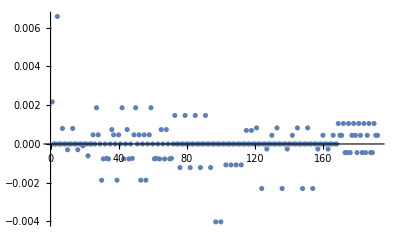

```mathematica
ListPlot[{list-listdft},PlotRange->All]
```

```mathematica
scale=list[[1]]/listdft[[1]]
```

1.017913808605515

```mathematica
listdft;
```

{0.12130489164836961,0.,0.,-0.020046798659570576,0.,0.,0.00055067657387175713,0.,0.,0.00025059263706886229,0.,0.,0.00055067657387175713,0.,0.,0.00025059263706886229,0.,0.,0.00008943268500049065,0.,0.,0.00061198692184502373,0.,0.,-0.0082358454650219536,0.,-0.016380854829541786,-0.0082358454650219536,0.,0.016380854829541786,0.00077584050549948122,0.,0.00071784960179932544,0.00077584050549948122,0.,-0.00071784960179932544,-0.0082358454650219536,0.,0.016380854829541786,-0.0082358454650219536,0.,-0.016380854829541786,0.00077584050549948122,0.,-0.00071784960179932544,0.00077584050549948122,0.,0.00071784960179932544,-0.0082358454650219536,-0.016380854829541786,0.,-0.0082358454650219536,0.016380854829541786,0.,-0.0082358454650219536,0.016380854829541786,0.,-0.0082358454650219536,-0.016380854829541786,0.,0.00077584050549948122,0.00071784960179932544,0.,0.00077584050549948122,-0.00071784960179932544,0.,0.00077584050549948122,-0.00071784960179932544,0.,0.00077584050549948122,0.00071784960179932544,0.,-0.00075316460406704548,0.,0.,0.0011810416783674051,0.,0.,-0.00075316460406704548,0.,0.,0.0011810416783674051,0.,0.,-0.00075316460406704548,0.,0.,0.0011810416783674051,0.,0.,-0.00075316460406704548,0.,0.,0.0011810416783674051,0.,0.,0.0027430354135428952,0.,0.,0.0027430354135428952,0.,0.,0.00089482081109805694,0.,0.,0.00089482081109805694,0.,0.,0.00089482081109805694,0.,0.,0.00089482081109805694,0.,0.,-0.00069802362433010539,0.,0.,-0.00069802362433010539,0.,0.,-0.013578129877862513,0.,0.,0.0029458952009150598,0.,0.,0.00030217812602073037,0.,0.,-0.00044705794372735343,0.,0.,-0.013578129877862513,0.,0.,0.0029458952009150598,0.,0.,0.00030217812602073037,0.,0.,-0.00044705794372735343,0.,0.,-0.013578129877862522,0.,0.,0.0029458952009150598,0.,0.,-0.013578129877862522,0.,0.,0.0029458952009150598,0.,0.,0.00030217812602073037,0.,0.,-0.00044705794372735343,0.,0.,0.00030217812602073037,0.,0.,-0.00044705794372735343,0.,0.,-0.0012692941308080899,-0.00057376636067325816,-0.00057376636067325816,-0.0012692941308080899,0.00057376636067325816,0.00057376636067325816,-0.0012692941308080899,0.00057376636067325816,-0.00057376636067325816,-0.0012692941308080899,-0.00057376636067325816,0.00057376636067325816,-0.0012692941308080899,-0.00057376636067325816,0.00057376636067325816,-0.0012692941308080899,0.00057376636067325816,-0.00057376636067325816,-0.0012692941308080899,0.00057376636067325816,0.00057376636067325816,-0.0012692941308080899,-0.00057376636067325816,-0.00057376636067325816}

```mathematica
slist=list/scale;
```

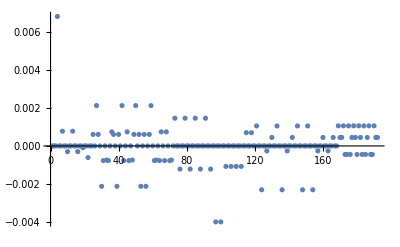

```mathematica
ListPlot[{slist-listdft},PlotRange->All]
```

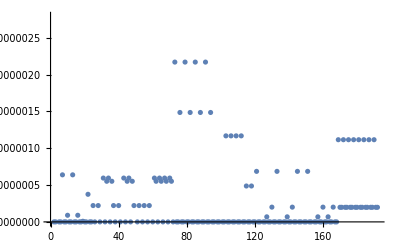

-1.68706×10^-8

```mathematica
ListPlot[(list-listdft)^2]
Total@@{slist-listdft}
```

```mathematica
Simplify[h[[1]][h[[2]][x]]]
```

1/x

{{x,1/x,1-x,1/(1-x),(-1+x)/x,x/(-1+x)},{1/x,x,1/(1-x),1-x,x/(-1+x),(-1+x)/x},{1-x,(-1+x)/x,x,x/(-1+x),1/x,1/(1-x)},{1/(1-x),x/(-1+x),1/x,(-1+x)/x,x,1-x},{(-1+x)/x,1-x,x/(-1+x),x,1/(1-x),1/x},{x/(-1+x),1/(1-x),(-1+x)/x,1/x,1-x,x}}

```mathematica
Table[Table[Simplify[h[[i]][h[[j]][x]]],{i,1,6}],{j,1,6}]
```

{{x,1/x,1-x,1/(1-x),(-1+x)/x,x/(-1+x)},{1/x,x,(-1+x)/x,x/(-1+x),1-x,1/(1-x)},{1-x,1/(1-x),x,1/x,x/(-1+x),(-1+x)/x},{1/(1-x),1-x,x/(-1+x),(-1+x)/x,x,1/x},{(-1+x)/x,x/(-1+x),1/x,x,1/(1-x),1-x},{x/(-1+x),(-1+x)/x,1/(1-x),1-x,1/x,x}}

#### Groups

A group is an algebraic structure that combines two elements to make a third and satifies the four group axioms: i) identity, ii) closure, iii) associativity, and iv) invertibility.

Example
h is a group of five functions, with the following multiplication table:

```mathematica
h={#&,1/#&,1-#&,1/(1-#)&,(#-1)/#&,#/(#-1)&};
TableForm[multiplicationTable=Table[Simplify[h[[i]][h[[j]][x]]],{i,1,6},{j,1,6}]]
```

x | 1/x | 1-x | 1/(1-x) | (-1+x)/x | x/(-1+x)
1/x | x | 1/(1-x) | 1-x | x/(-1+x) | (-1+x)/x
1-x | (-1+x)/x | x | x/(-1+x) | 1/x | 1/(1-x)
1/(1-x) | x/(-1+x) | 1/x | (-1+x)/x | x | 1-x
(-1+x)/x | 1-x | x/(-1+x) | x | 1/(1-x) | 1/x
x/(-1+x) | 1/(1-x) | (-1+x)/x | 1/x | 1-x | x

Find a function invariant under this group
fsym(x)≡1n∑H∈f(H(x))

```mathematica
Clear[f]
```

```mathematica
symmetrize[f_]:=With[{n=Length[h]},Function[{x},(1/n)* Total@Map[Composition[f,#][x]&,h]]]
```

```mathematica
f[x_]:=x;
fSym=symmetrize[f];
fSym[x]
```

1/6 (1+1/(1-x)+1/x+(-1+x)/x+x/(-1+x))

```mathematica
Table[Simplify[fSym[h[[i]][x]]==fSym[h[[j]][x]]],{i,1,6},{j,1,6}]//TableForm
```

True | True | True | True | True | True
True | True | True | True | True | True
True | True | True | True | True | True
True | True | True | True | True | True
True | True | True | True | True | True
True | True | True | True | True | True

```mathematica
f[x_]:=Exp[x-x^2]
fSym=symmetrize[f];
Table[Simplify[fSym[h[[i]][x]]==fSym[h[[j]][x]]],{i,1,6},{j,1,6}]//TableForm
```

True | True | True | True | True | True
True | True | True | True | True | True
True | True | True | True | True | True
True | True | True | True | True | True
True | True | True | True | True | True
True | True | True | True | True | True

```mathematica
f[x_]:=Exp[i*x]^x
fSym=symmetrize[f];
Table[Simplify[fSym[h[[i]][x]]==fSym[h[[j]][x]]],{i,1,6},{j,1,6}]//TableForm
```

True | True | True | True | True | True
True | True | True | True | True | True
True | True | True | True | True | True
True | True | True | True | True | True
True | True | True | True | True | True
True | True | True | True | True | True

Example 2

Operations are
1) Cn rotation about an n-fold axis
2) Sn improper rotation n-fold axis
3) E invariance under translation
4) i inversion
5)

```mathematica
t={#[[1]],-#[[2]]}&
```

{#1⟦1⟧,-#1⟦2⟧}&

```mathematica
t[{x,y}]
```

{x,-y}

```mathematica
id={#[[1]],#[[2]],#[[3]]}&
inverse={-#[[1]],-#[[2]],-#[[3]]}&
xreflect={-#[[1]],#[[2]],#[[3]]}&
yreflect={#[[1]],-#[[2]],#[[3]]}&
zreflect={#[[1]],#[[2]],-#[[3]]}&
```

{#1⟦1⟧,#1⟦2⟧,#1⟦3⟧}&

{-#1⟦1⟧,-#1⟦2⟧,-#1⟦3⟧}&

{-#1⟦1⟧,#1⟦2⟧,#1⟦3⟧}&

{#1⟦1⟧,-#1⟦2⟧,#1⟦3⟧}&

{#1⟦1⟧,#1⟦2⟧,-#1⟦3⟧}&

```mathematica
h={id,xreflect,yreflect,zreflect,inverse};
TableForm[multiplicationTable=Table[Simplify[h[[i]][h[[j]][{x,y,z}]]],{i,1,Length@h},{j,1,Length@h}]]
```

x
y
z | -x
y
z | x
-y
z | x
y
-z | -x
-y
-z
-x
y
z | x
y
z | -x
-y
z | -x
y
-z | x
-y
-z
x
-y
z | -x
-y
z | x
y
z | x
-y
-z | -x
y
-z
x
y
-z | -x
y
-z | x
-y
-z | x
y
z | -x
-y
z
-x
-y
-z | x
-y
-z | -x
y
-z | -x
-y
z | x
y
z

```mathematica
f[{x_,y_,z_}]:={x^2,y,z};
fSym=symmetrize[f];
fSym[{x,y,z}]
```

{x^2,y/5,z/5}

```mathematica
id=#&
inverse=-#&

h={id,inverse};
TableForm[multiplicationTable=Table[Simplify[h[[i]][h[[j]][x]]],{i,1,Length@h},{j,1,Length@h}]]
```

#1&

-#1&

x | -x
-x | x

```mathematica
symmetrize[f_]:=With[{n=Length[h]},Function[{x},(1/n)* Total@Map[Composition[f,#][x]&,h]]]

f[x_]:=x^2;
fSym=symmetrize[f];
fSym[x]

Table[fSym[h[[i]][x]]==fSym[h[[j]][x]],{i,1,Length@h},{j,1,Length@h}]//TableForm
```

x^2

True | True
True | True

```mathematica
invariant1[x_]:=(x^2-x+1)^3/(x^2 (x-1)^2)
Simplify[symmetrize[invariant1][x]]===Simplify[invariant1[x]]
```

False

```mathematica
symmetrize[invariant1][x]
Simplify[invariant1[x]]
```

1/2 (((1-x+x^2)^3)/((-1+x)^2 x^2)+((1+x+x^2)^3)/((-1-x)^2 x^2))

((1-x+x^2)^3)/((-1+x)^2 x^2)

```mathematica
f[x_]:=x^2
fSym=symmetrize[f];

Table[fSym[h[[i]][x]]===fSym[h[[j]][x]],{i,1,Length@h},{j,1,Length@h}]//TableForm
```

True | True
True | True

```mathematica
invariant1[x_]:=(x^2-x+1)^3/(x^2 (x-1)^2)
Simplify[symmetrize[invariant1][x]===invariant1[x]]
```

False

```mathematica
symmetrize[invariant1][x]
```

1/2 (((1-x+x^2)^3)/((-1+x)^2 x^2)+((1+x+x^2)^3)/((-1-x)^2 x^2))

```mathematica
Clear[x]
```

```mathematica
Evaluate[h[[2]][x]]
```

-x

```mathematica
fSym[h[[1]][x]]
fSym[h[[2]][x]]
```

0

0

```mathematica
3==4
```

False